```mathematica
SetDirectory["~/bin/tracts_v0.3/example"](*Set to directory containing output files*)
colors={Red,Blue};



models={"out","out2"};
```

/Users/gravel/bin/tracts_v0.3/example

```mathematica
(*Make legend*)
(*legend elements*)
symbols={"●","▲","■"};
legelem[name_,height_,color_,symbol_]:=Inset[Graphics[{color,Thickness[0.03],Line[{{1.5,0},{4,0}}],Text[Style[symbol<>" "<>symbol<>" "<>symbol,FontSize->Scaled[.1]],{6,0}],Text[Style[name,FontSize->Scaled[.2]],{-.4,0}]}],{1,height},{0,0},{2,.5}]

leg2=Graphics[{GrayLevel[1],EdgeForm[{Thickness[0.001],GrayLevel[0]}],Rectangle[{-.85,-.77},{-0.38956521739130423,-0.5599999999999984}],Inset[Graphics[
{{Text[Style["Anc.   Model  Data",FontSize->Scaled[.075]],{1.6,1.8},{0,0}],

(*{Inset[Graphics[{Thickness[0.004],RGBColor[0.5,0,0.5],Thickness[0.03],Line[{{0,0},{.8,0}}],Dashing[{Large,Medium}],Line[{{.8,0},{2,0}}]}       ],{0.08,0.04},{Left,Bottom},{1,1}],Text[Style["YRI (Projected)",Medium],{1.2100000000000002,0.54},{-1,0},{1,0}]},

{Inset[Graphics[{Thickness[0.004],RGBColor[1,0,0],Thickness[0.03],Line[{{0,0},{.8,0}}],Dashing[{Large,Medium}],Line[{{.8,0},{2,0}}]}],{0.08,0.54},{Left,Bottom},{1,1}],Text[Style["CHBJPT (Projected)",Medium],{1.2100000000000002,1.042},{-1,0},{1,0}]},

{Inset[Graphics[{Thickness[0.004],RGBColor[1,0,0],Thickness[0.03],Line[{{0,0},{.8,0}}],Dashing[{Large,Medium}],Text[Style["(",Large],{.9,0}],Text[Style[")",Large],{1.93,0}],Line[{{.95,0},{1.95,0}}]}],{0.08,1.04},{Left,Bottom},{1,1}],Text[Style["CEU (Projected)",Medium],{1.21,1.042},{-1,0},{1,0}]},
*)
(*{Inset[Graphics[{RGBColor[1,0,0],Thickness[0.02],Line[{{0,0},{.8,0}}],Dashing[{.19,Medium}],
Text[Style["(",Large],{.9,0}],Text[Style[")",Large],{2.38,0}],Line[{{.95,0},{2.38,0}}]   }],{0.08,1.04},{Left,Bottom},{2,1}],Black,Text[Style["SYN",Medium],{1.5,1.52}],
Inset[Graphics[{RGBColor[1,0,0],Thickness[0.02],Line[{{0,0},{.8,0}}],Dashing[{Tiny,Medium}],
Text[Style["(",Large],{.9,0}],Text[Style[")",Large],{2.38,0}],Line[{{.95,0},{2.38,0}}]   }],{0.08,0.8},{Left,Bottom},{2,1}]},
Black,Text[Style["NONSYN",Medium],{1.5,1.30}],
Text[Style["}",FontSize->36],{1.8,1.4}]},{Text[Style["CEU",FontSize->18],{2.1,1.4}]
*)
legelem["AFR",1.2,colors[[2]],symbols[[2]]],
legelem["EUR",1.5, colors[[1]],symbols[[1]]]


},{}},AspectRatio->1.0952380952380953,PlotRange->{{-0.1,3.26},{-0.1,3.5799999999999996}}],{-1,-1},{Left,Bottom},{0.7304347826086958,0.8000000000000002}]}]
```

-Graphics-

```mathematica
(*Convert bins to Morgans for Plotting*)
plotpop[name_]:=Module[{bins,expects,data,migstot,alphatot,dots,rect,arrows,arrows2,font,piecharts,piechartstab,texts,plot2,ticks,migs,symbols,vals,range},

(*import data*)
bins=100*Import [name<>"_bins","TSV"][[1]];
expects=Import [name<>"_pred","TSV"];
data=Import [name<>"_dat","TSV"];
migs=Import [name<>"_mig","TSV"];


maxT=Dimensions[migs][[1]];(*length of migration process*)
npops=Dimensions[migs][[2]]; (*number of ancestral populations*)
(*get the total proportion of ancestry after generation i*)
m=Apply[Plus,Transpose[migs]];
alphas=Table[Sum[migs[[g,pop]] Apply[Times,(1-m)[[i;;g-1]]],{g,i,maxT}],{i,1,maxT},{pop,1,npops}];

symbols={"●","▲","■"};

(*To generate the plot, calculate some intermediary quantities*)
alphatot=Table[If[i==0,0*alphas[[1;;,1]],Sum[alphas[[-1;;1;;-1,j]],{j,1,i}]],{i,0,npops}]; (*Total ancestry at each generation*)
dots=Graphics[Table[{colors[[j]],Disk[{i,1+j/2},Sqrt[migs[[-1;;1;;-1]][[i,j]]]/3]},{i ,1, Length[migs]},{j,1,Length[migs[[1]]]}]];


arrows=Table[vals=migs[[-1;;1;;-1]][[i]];If[Apply[Plus,vals]==0,,{Black,Thick,Arrowheads[.015],Arrow[{{i,1.3},{i,1}}]}],{i ,1, maxT}];
arrows2=Select[arrows,Length[#]>2&];

font=20;
piecharts=GraphicsRow[Table[ vals=migs[[-1;;1;;-1]][[i]];If[Apply[Plus,vals]==0,,PieChart[vals,ChartStyle->colors,ImageSize->20*Sqrt[m[[-1;;1;;-1]][[i]]]] ],{i ,1, Length[migs]}]];
piechartstab=Table[ Inset[vals=migs[[-1;;1;;-1]][[i]];If[Apply[Plus,vals]==0,,PieChart[vals,ChartStyle->colors,ImageSize->35*Sqrt[m[[-1;;1;;-1]][[i]]]] ],{i,1.3},{0,0}],{i ,1, Length[migs]}];
texts={Inset[Graphics[Arrow[{{0,1},{1,1}}]],ImageScaled[{.57,.1}],{.5,1},.7*Length[migs]],Inset[Style[Text["Time",Background->White],font],ImageScaled[{.55,.09}]],Inset[Style[Text["today"],font],ImageScaled[{.95,.1}]],Inset[Style[Text[ToString[maxT]<>" GA"],font],ImageScaled[{0.17,.1}]],Inset[Style[Text["Magnitude and origin\n of migrants"],font],ImageScaled[{.5,.86}]],Inset[Rotate[Style[Text["Ancestry\nproportion"],font],Pi/2],ImageScaled[{0.05,.45}]],Inset[Style[Text[0],font],ImageScaled[{0.12,.15}]],Inset[Style[Text[1],font],ImageScaled[{0.12,.66}]]};

texts={Inset[Graphics[Arrow[{{0,1},{1,1}}]],ImageScaled[{.6,.06}],{.5,1},.7*Length[migs]],Inset[Style[Text["Time",Background->White],font],{maxT/2,-0.17}],Inset[Style[Text["today"],font],{maxT-.5,-0.17}],Inset[Style[Text[ToString[maxT]<>" GA"],font],{1.3,-0.17}],Inset[Style[Text["Magnitude and origin\n of migrants"],font],ImageScaled[{.5,.86}]],Inset[Rotate[Style[Text["Ancestry\nproportion"],font],Pi/2],{0.0,.4}],Inset[Style[Text[0],font],{0.5,0}],Inset[Style[Text[1],font],{0.5,1}]};
(*Inset[piechartstab[[1]],{1,-.3},{0,0},1.5]*)
ticks=Table[{Black,Line[{{i,.1},{i,0}}]},{i ,1, npops+1}];
plot2=ListPlot[alphatot,Joined->True,InterpolationOrder->0,Filling->Table[i->{{i+1},colors⟦i⟧},{i ,1, npop}],FillingStyle->colors,PlotStyle->None,Axes->{False,False},Epilog->Join[arrows2,piechartstab,texts,ticks],PlotRange->{{-1.8,Automatic},{-.3,1.9}},AspectRatio->.3 ,Ticks->{Automatic}];


range=2000;
(*Plot the histogram of model vs data using the model data generated by python*)
(*Hack to get around a Mathematica bug: plot theory and data separately*)
plottheories=Table[Transpose[{bins[[1;;-2]],expects[[popnum]][[1;;-2]]}],{popnum,1,npops}];
lowbound[mean_,alpha_]:=Module[{i,fun},fun=CDF[PoissonDistribution[mean]]; For[i=0,True,i++,If[fun[i]>alpha/2,Return[Max[i-1,0]]]]];
highbound[mean_,alpha_]:=Module[{i,fun},fun=CDF[PoissonDistribution[mean]]; For[i=0,True,i++,If[fun[i]>1-alpha/2,Return[i]]]];


high=Table[Map[{#[[1]],highbound[#[[2]],0.3173105078629141]} &, plottheories⟦pop⟧+10^-9],{pop,1,npops}];
low=Table[Map[{#[[1]],lowbound[#[[2]],0.3173105078629141]} &, plottheories⟦pop⟧+10^-9],{pop,1,npops}];


expect=Table[ListLogPlot[{plottheories[[pop]],high[[pop]]+10^-9,low[[pop]]+10^-8},Joined->{True,False,False},PlotRange->{0.4,range},Filling->{1->{{3},Directive[Opacity[.2],colors[[pop]]]},1->{{2},Directive[Opacity[.2],colors[[pop]]]}},PlotMarkers->{""}, PlotStyle->{{Thick,colors[[pop]]}, {}, {Thickness[10^-8]}} ],{pop,1,npops}];


plotdats=Table[{Transpose[{bins[[1;;-2]],data[[popnum]][[1;;-2]]}]},{popnum,1,npops}];



zeroes[dat_,bins_,val_,shift_]:=Module[{temp,i,flag,last},
last=Length[dat];
For[i=Length[dat],i>0,i--,If[dat[[i]]!=0,last=i;Break[]]];
temp={};
For[i=1,i≤last,i++,If[dat[[i]]==0,AppendTo[temp,{bins[[i]],val}]]

](*;If[temp=={},temp={{}}]*);temp];

zers=Table[zeroes[data[[i]][[1;;-2]],bins,0.4,0],{i,1,npops}];

(*It's odd to do this as a table, but it circumvents a bug in Mathematica with logplots. Because there's also a bug in combining the log-plots, we set the Plotrange by hand in dats.*)

datstab=Table[ListLogPlot[plotdats[[i]],Joined->False,PlotRange->{0.4,range},PlotStyle->Map[{Thick,#}&,colors[[1;;npops]]][[i]],PlotMarkers->{"●","▲","■"}[[i]],AxesOrigin->{0,.4}],{i,1,npops}];
dats=Show[datstab,PlotRange->{-.5,8}];
(*expect=ListLogPlot[plottheories,Joined->True,PlotRange->{0.4,1000},PlotStyle->Map[{Thick,#}&,{colors[[1]],colors[[1]],colors[[2]],colors[[2]],colors[[3]],colors[[3]]}]];*)

zerplot=ListLogPlot[zers,PlotRange->{{0,Max[bins]},{.1,0.74}},PlotStyle->Map[{Thick,#}&,colors[[1;;npops]]],PlotMarkers->{ ○,△,□},Axes->{True,False}];

zerArr=Graphics[Table[{colors[[i]],Map[{Arrowheads[.02], Arrow[{{# [[1]],-.5},{#[[1]],-.99}}]}&,zers[[i]]]},{i,1,npops}]];
lastzers={};
For[i=1,i≤npops,i++,If[data[[i]][[-1]]==0,AppendTo[lastzers,{colors[[i]],Arrowheads[.02],Arrow[{{bins[[-1]]+(bins[[2]]-bins[[1]])/4*(i-2),-.5},{bins[[-1]]+(bins[[2]]-bins[[1]])/4*(i-2),-.99}}]}] ]    ];
lastzerplot=Graphics[lastzers];
central=Show[dats,expect(*,zerArr,lastzerplot*)(*,fullplot,expectfull*),Epilog->{Inset[leg2,ImageScaled[{.7,.9}],ImageScaled[{0.5,0.5}],{700,8}]},FrameLabel->{"Tract Length (cM)","Number of tracts"},Frame->{True,True,False,False},FrameStyle->Directive[22],ImageSize->{700,400}];


final=GraphicsColumn[{central,plot2},Alignment->Top]


]
```

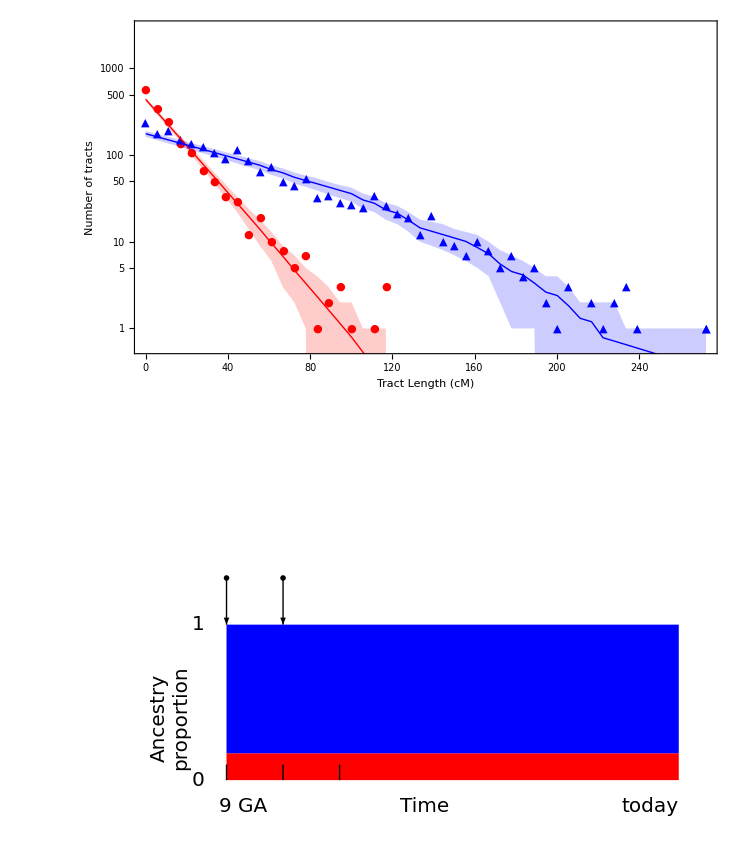
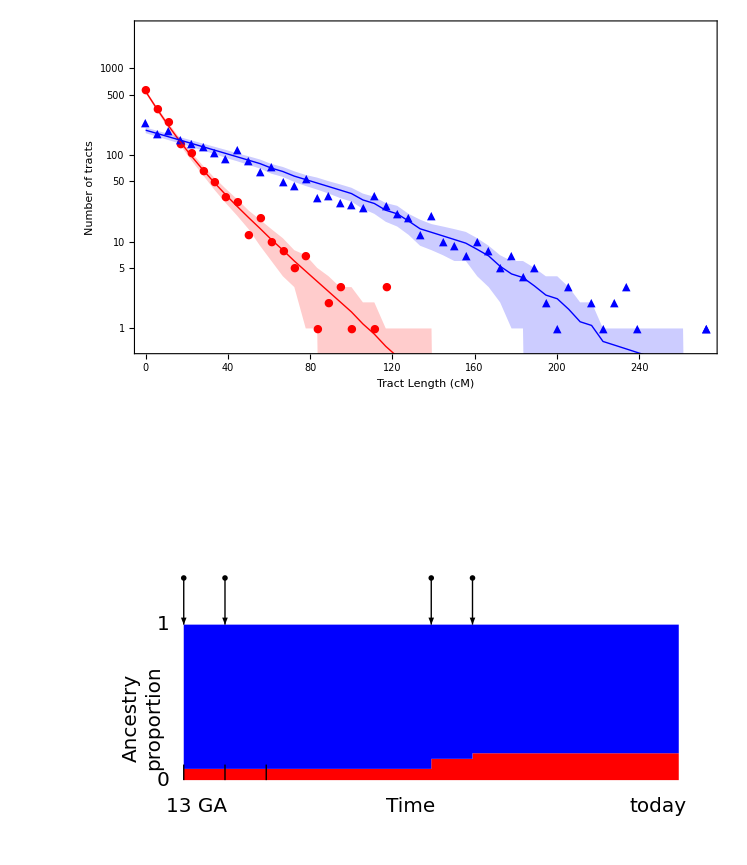

```mathematica
allpops=Map[plotpop,models]
```